## Generate random CA rule, data, and neural net

### Wolfram Classes of ECAs

```mathematica
CAclasses = {1,2,2,2,2,2,2,2,1,2,2,2,2,2,2,2,2,2,3,2,2,2,3,2,2,2,2,2,2,2,3,2,1,2,2,2,2,2,2,2,1,3,2,2,2,3,2,2,2,2,2,2,2,2,4,2,2,2,2,2,3,2,2,2,1,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,2,2,3,2,2,3,3,2,2,2,2,2,1,3,2,2,2,3,3,2,2,3,3,3,2,2,4,2,2,2,2,2,2,2,2,2,3,3,3,2,4,2,3,2,1,3,2,2,2,2,2,3,1,4,2,2,2,2,2,2,2,2,3,4,2,3,3,3,2,3,2,2,2,2,2,2,1,3,2,2,2,3,2,2,1,3,2,2,2,2,2,2,2,2,2,2,2,2,3,3,2,2,2,2,2,2,2,2,1,4,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,1,1,2,2,1,1,2,2,2,2,2,2,2,2,1,1,1,1,1,1,1,1};
```

### Functions for creating net and random datasets (ECAs)

```mathematica
RandomRule[n_Integer,W_Integer,H_Integer]:=Image[1-CellularAutomaton[n,RandomInteger[1,W],H-1],ImageSize->{UpTo@256,UpTo@256}]
net[W_Integer,H_Integer]:=NetInitialize@NetChain[{ConvolutionLayer[16,{2,3}],Ramp,PoolingLayer[{H,W}-{1,2}],FlattenLayer[],LinearLayer[256],SoftmaxLayer[]},"Input"->NetEncoder[{"Image",{W,H},"ColorSpace"->"Grayscale"}],"Output"->NetDecoder[{"Class",Range[0,255]}]]
netTwoC[W_Integer,H_Integer]:=NetInitialize@NetChain[{ConvolutionLayer[16,{2,3}],Ramp, ConvolutionLayer[16,{2,3}],Ramp,PoolingLayer[{H,W}-{2,4}],FlattenLayer[],512,4,SoftmaxLayer[]},"Input"->NetEncoder[{"Image",{W,H},"ColorSpace"->"Grayscale"}],"Output"->NetDecoder[{"Class",Range[1,4]}]]
data[W_Integer,H_Integer,n_Integer]:=Table[RandomRule[i,W,H]->CAclasses[[i+1]],{i,RandomChoice[Range[0,255],n]}]
```

### Functions for creating net and datasets (1D totalistic CAs)

```mathematica
gen3T [p_Integer,W_Integer,H_Integer]:=Image[CellularAutomaton[{p, {3,1}},RandomInteger[1,W],H-1],ImageSize->{W,H}]
net3T[W_Integer,H_Integer]:=NetInitialize@NetChain[{ConvolutionLayer[16,{2,3}],Ramp,PoolingLayer[{H,W}-{1,2}],FlattenLayer[],LinearLayer[256],LinearLayer[256],SoftmaxLayer[]},"Input"->NetEncoder[{"Image",{W,H},"ColorSpace"->"Grayscale"}],"Output"->NetDecoder[{"Class",Range[0,255]}]]
data3T2[W_Integer,H_Integer,n_Integer]:=Table[gen3T[i,W,H]->4,{i,RandomChoice[{1635,1815,2007,2043,2049,1388,1041},n]}]
```

```mathematica
gen4T [p_Integer,W_Integer,H_Integer]:=Image[CellularAutomaton[{p, {4,1}},RandomInteger[1,W],H-1],ImageSize->{W,H}]
data4T[W_Integer,H_Integer]:=Table[gen4T[1004600,W,H]->4,{n, 0, 2048}]
```

```mathematica
TCA4test=data4T[120,40];
```

```mathematica
gen5T [p_Integer,W_Integer,H_Integer]:=ArrayPlot[CellularAutomaton[{p, {5,1}},RandomInteger[1,W],H-1],ImageSize->{W,H},Frame->False]
data5T[W_Integer,H_Integer,n_Integer]:=Table[gen5T[i,W,H]->i,{i,RandomChoice[Range[0,1220703125],n]}]
```

```mathematica
gen5T2 [p_Integer,W_Integer,H_Integer]:=Image[CellularAutomaton[{p, {5,1}},RandomInteger[1,W],H-1],ImageSize->{W,H}]
data5T2[W_Integer,H_Integer,n_Integer]:=Table[gen5T[i,W,H]->i,{i,RandomChoice[Range[0,1220703125],n]}]
```

### k=2, r=2 totalistic

```mathematica
gen2r2 [p_Integer,W_Integer,H_Integer]:=ArrayPlot[CellularAutomaton[{p, {2,1},2},RandomInteger[1,W],H-1],ImageSize->{256,128}, Frame->False]
data2r2c4[W_Integer,H_Integer,n_Integer]:=Table[gen2r2[i,W,H]->4,{i,RandomChoice[{20,52},n]}]
data2r2c3[W_Integer,H_Integer,n_Integer]:=Table[gen2r2[i,W,H]->3,{i,RandomChoice[{2,6,10,12,14,18,22,26,28,30,34,38,42,44,46,50},n]}]
data2r2c2[W_Integer,H_Integer,n_Integer]:=Table[gen2r2[i,W,H]->2,{i,RandomChoice[{8,24,56},n]}]
data2r2c1[W_Integer,H_Integer,n_Integer]:=Table[gen2r2[i,W,H]->1,{i,RandomChoice[{0,4,16,32,36,40,48,54,58,60,62},n]}]
genData2r2[W_Integer,H_Integer,n_Integer]:=Join[data2r2c4[W,H,n], data2r2c3[W,H,n],data2r2c2[W,H,n],data2r2c1[W,H,n]]
```

### k=2, r=2 non-totalistic

```mathematica
genk2r2 [p_Integer,W_Integer,H_Integer]:=Image[CellularAutomaton[{p, 2,2},RandomInteger[1,W],H-1],ImageSize->{W,H}]
datak2r2[W_Integer,H_Integer,n_Integer]:=Table[genk2r2[i,W,H]->i,{i,RandomChoice[Range[0,4294967295],n]}]
```

### k=3, r=2 totalistic

```mathematica
genk3r2 [p_Integer,W_Integer,H_Integer]:=Image[CellularAutomaton[{p, {3,1},2},RandomInteger[1,W],H-1],ImageSize->{W,H}]
datak3r2[W_Integer,H_Integer,n_Integer]:=Table[genk3r2[i,W,H]->i,{i,RandomChoice[Range[0,177146],n]}]
```

### k=4, r=1 totalistic

```mathematica
genk4r1 [p_Integer,W_Integer,H_Integer]:=ArrayPlot[CellularAutomaton[{p, {4,1}},RandomInteger[1,W],H-1],ImageSize->{W,H}, Frame->False]
datak4r1[W_Integer,H_Integer,n_Integer]:=Table[genk4r1[i,W,H]->i,{i,RandomChoice[Range[0,1048575],n]}]
```

### k=4, r=2 totalistic

```mathematica
genk4r2 [p_Integer,W_Integer,H_Integer]:=Image[CellularAutomaton[{p, {4,1},2},RandomInteger[1,W],H-1],ImageSize->{W,H}]
datak4r2[W_Integer,H_Integer,n_Integer]:=Table[genk4r2[i,W,H]->i,{i,RandomChoice[Range[0,4294967295],n]}]
```

### Sample dataset

```mathematica
sampleWCA=data[120,40, 10]
```

{-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→3}

## Train net

```mathematica
trainedWCA=net[120,40]
```

NetChain[<>]

```mathematica
trainedWCA=NetTrain[trained,data[120,40,256*128],MaxTrainingRounds->1000,BatchSize->256*4,TargetDevice->"CPU"]
```

NetChain[<>]

```mathematica
Export["trainedWCA.wlnet",trainedWCA]
```

trainedWCA.wlnet

## Training Two-Layer CNN Attempt I

```mathematica
newData=data[120,60,256*256];
```

```mathematica
RandomSample[newData,5]
```

{-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→3,-Graphics-→2}

```mathematica
trained2C=netTwoC[120,60]
```

NetChain[<>]

```mathematica
trained2C=NetTrain[trained2C,newData,MaxTrainingRounds->1000,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory","WolframCAClassifier"}]
```

NetChain[<>]

```mathematica
newTestData=data[120,60,64*64];
```

```mathematica
cm2C=ClassifierMeasurements[trained2C,newTestData];
Quantity[100*cm2C["Accuracy"],"Percent"]
```

100. %

```mathematica
newTestData3T=data3T2[120,60,1000];
```

```mathematica
RandomSample[newTestData3T,5]
```

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4}

```mathematica
newTest3T=Keys@newTestData3T;
cm2C3T=ClassifierMeasurements[trained2C,newTestData3T];
Quantity[100*cm2C3T["Accuracy"],"Percent"]
```

18.5 %

```mathematica
newTestData3T2=data3T2[120,60,4096];
```

```mathematica
RandomSample[newTestData3T2,5]
```

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4}

```mathematica
cm2C3T=ClassifierMeasurements[trained2C,newTestData3T2];
Quantity[100*cm2C3T["Accuracy"],"Percent"]
```

15.6006 %

```mathematica
florp=Keys@RandomSample[newTestData3T2,5];
Thread[florp->trained2C[florp]]
```

{-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→4,-Graphics-→4}

## Training Two-Layer CNN Attempt II

```mathematica
newDataECAc2=data[120,60,128*128];
newData3Tc2=data3T2[120,60,64*64];
newData4Tcc=data4T[120,60];
fullDatac2=Join[newDataECAc2,newData3Tc2,newData4Tc2];
Length[fullDatac2]
RandomSample[fullDatac2,10]
```

22529

{-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→2}

```mathematica
trained2C2=netTwoC[120,60]
```

NetChain[<>]

```mathematica
trained2C2=NetTrain[trained2C2,fullDatac2,MaxTrainingRounds->10,BatchSize->256*4,TargetDevice->"CPU",TrainingProgressCheckpointing->{"Directory","WolframCAClassifier"}]
```

NetChain[<>]

```mathematica
testDataECAc2=data[120,60,2048];
testData3Tc2=data3T2[120,60,2048];
testData4Tcc=data4T[120,60];
fullTestc2=Join[testDataECAc2,testData3Tc2,testData4Tcc];
Length[fullTestc2]
RandomSample[fullTestc2,10]
```

6145

```mathematica
RandomSample[fullTestc2,10]
```

{-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→3}

```mathematica
cm2C2Test=ClassifierMeasurements[trained2C2,fullTestc2];
Quantity[100*cm2C2Test["Accuracy"],"Percent"]
```

98.9585 %

#### Testing k=5, r=1 totalistic rule examples

```mathematica
test5T=data5T[120,60,2048];
```

```mathematica
flerb=RandomSample[test5T,5];
Thread[flerb->trained2C2[Keys@flerb]]
```

{(-Graphics-→53712566)→2,(-Graphics-→522064368)→2,(-Graphics-→116130464)→2,(-Graphics-→1129050528)→4,(-Graphics-→262354440)→2}

```mathematica
check5T=Keys@RandomSample[test5T,10];
Thread[check5T->trained2C2[check5T]]
```

{-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→4,-Graphics-→3}

```mathematica
check5T2=Keys@RandomSample[test5T,10];
Thread[check5T2->trained2C2[check5T2]]
```

{-Graphics-→3,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→4,-Graphics-→3,-Graphics-→4,-Graphics-→2,-Graphics-→4}

```mathematica
check5T3=Keys@RandomSample[test5T,9];
Thread[check5T3->trained2C2[check5T3]]
```

{-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→2,-Graphics-→4,-Graphics-→3,-Graphics-→3,-Graphics-→4,-Graphics-→3}

```mathematica
check5T4=Keys@RandomSample[test5T,9];
Thread[check5T4->trained2C2[check5T4]]
```

{-Graphics-→3,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→4,-Graphics-→3,-Graphics-→2,-Graphics-→3,-Graphics-→3}

```mathematica
test5TImg=data5T2[120,60,1024];
```

```mathematica
check5TImg=Keys@RandomSample[test5TImg,9];
Thread[check5TImg->trained2C2[check5TImg]]
```

{-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→4,-Graphics-→4,-Graphics-→4}

```mathematica
test2R2=genData2r2[120,60,256];
Length[test2R2]
```

1024

```mathematica
cm2C2R2=ClassifierMeasurements[trained2C2,test2R2];
Quantity[100*cm2C2R2["Accuracy"],"Percent"]
```

47.5586 %

```mathematica
entropyImages=RandomSample[Keys[test5T],500];
entropies=trained2C2[entropyImages,"Entropy"];
highEnt=entropyImages[[Ordering[entropies,-6]]];
lowEnt=entropyImages[[Ordering[entropies,10]]];
Thread[highEnt->trained2C2[highEnt]]
```

{-Graphics-→3,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→4}

### Testing k=2, r=2 non-totalistic rules

```mathematica
testDatak2r2=datak2r2[120,60,1024];
```

```mathematica
testk2r2=RandomSample[testDatak2r2, 5];
Thread[testk2r2->trained2C2[Keys@testk2r2]]
```

{(-Graphics-→2625858102)→3,(-Graphics-→4172604097)→4,(-Graphics-→2746718847)→3,(-Graphics-→2749386474)→2,(-Graphics-→2772996045)→2}

### Testing k=3, r=2 totalistic

```mathematica
trained2C2=Import["trained2C2.wlnet","WLNet"]
```

NetChain[<>]

```mathematica
testDatak3r2=datak3r2[120,60,5];
Thread[testDatak3r2->trained2C2[Keys@testDatak3r2]]
```

{(-Graphics-→40001)→3,(-Graphics-→111444)→2,(-Graphics-→45179)→4,(-Graphics-→78808)→3,(-Graphics-→28937)→4}

### Testing k=4, r=1 totalistic

```mathematica
testDatak4r1=datak4r1[120,60,5];
Thread[testDatak4r1->trained2C2[Keys@testDatak4r1]]
```

{(-Graphics-→1024863)→2,(-Graphics-→483330)→3,(-Graphics-→626304)→1,(-Graphics-→244401)→4,(-Graphics-→562075)→3}

```mathematica
weights=NetExtract[trained2C2,{"1","Weights"}];
weights2=NetExtract[trained2C2,{"3","Weights"}];
```

```mathematica
Dimensions[weights]
Dimensions[weights2]
```

{16,1,2,3}

{16,16,2,3}

```mathematica
ImageAdjust[Image[#,Interleaving->False]]&/@weights
ImageAdjust[Image[#,Interleaving->False]]&/@weights2
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

### Export trained nets

```mathematica
Export["trained2C.wlnet",trained2C,"WLNet"]
```

trained2C.wlnet

```mathematica
Export["trained2C.json", trained2C, "MXNet"]
```

trained2C.json

```mathematica
Export["trained2C2.wlnet", trained2C2, "WLNet"]
```

trained2C2.wlnet

```mathematica
Export["trained2C2.json", trained2C2, "MXNet"]
```

trained2C2.json

## Testing the trained network

### Accuracy on new ECA data

```mathematica
testData=data[120,40,256*256];
```

```mathematica
cmWCA2=ClassifierMeasurements[trainedWCA,testData];
Quantity[100*cm["Accuracy"],"Percent"]
```

99.7406 %

### Testing predictions on new data

```mathematica
testImgs=Keys@RandomSample[testData,15];
Thread[testImgs->trainedWCA[testImgs]]
```

{-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→2}

```mathematica
testImgs2=Keys@RandomSample[testData,15];
Thread[testImgs2->trainedWCA[testImgs2]]
```

{-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→1,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→2}

```mathematica
randomTest3 = RandomSample[testData, 15]
testImgs3=Keys@randomTest3;
Thread[testImgs3->trainedWCA[testImgs3]]
```

{-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→2}

{-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→2}

```mathematica
randomTest4 = RandomSample[testData, 15]
testImgs4=Keys@randomTest4;
Thread[testImgs4->trainedWCA[testImgs4]]
```

{-Graphics-→2,-Graphics-→1,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2}

{-Graphics-→2,-Graphics-→1,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2}

### Checking highest-entropy and lowest-entropy predictions in test set

```mathematica
entropyImages=RandomSample[Keys[testData],5000];
entropies=trainedWCA[entropyImages,"Entropy"];
highEnt=entropyImages[[Ordering[entropies,-10]]]
lowEnt=entropyImages[[Ordering[entropies,10]]]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Thread[highEnt->trainedWCA[highEnt]]
Thread[lowEnt->trainedWCA[lowEnt]]
```

{-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→2}

{-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2}

### Checking predictions on totalistic codes

#### Two-colour totalistic codes

```mathematica
code20table= Table[Image[CellularAutomaton[{n, {2,1}},RandomInteger[1,120],40],ImageSize->{256,128}],{n,0,15}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Thread[code20table->trainedWCA[code20table]]
```

{-Graphics-→1,-Graphics-→2,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→1,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→1}

#### Three-colour totalistic codes

```mathematica
code31table= Thread[Table[Image[CellularAutomaton[{n, {3,1}},RandomInteger[1,120],40],ImageSize->{256,128}]->n,{n,0,2186}]];
code31sample=RandomSample[code31table, 15]
code31test = Keys@code31sample;
Thread[code31test->trainedWCA[code31test]]
```

{-Graphics-→1635,-Graphics-→1307,-Graphics-→1891,-Graphics-→1913,-Graphics-→1766,-Graphics-→1857,-Graphics-→1032,-Graphics-→865,-Graphics-→1107,-Graphics-→1640,-Graphics-→453,-Graphics-→346,-Graphics-→590,-Graphics-→1098,-Graphics-→1820}

{-Graphics-→4,-Graphics-→4,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→1,-Graphics-→1,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→3}

```mathematica
code1635table= Thread[Table[Image[CellularAutomaton[{1635, {3,1}},RandomInteger[1,120],40],ImageSize->{256,128}],{n,0,5}]];
code2049table= Thread[Table[Image[CellularAutomaton[{2049, {3,1}},RandomInteger[1,120],40],ImageSize->{256,128}],{n,0,5}]];
code348table= Thread[Table[Image[CellularAutomaton[{348, {3,1}},RandomInteger[1,120],40],ImageSize->{256,128}],{n,0,5}]];
code1815table= Thread[Table[Image[CellularAutomaton[{1815, {3,1}},RandomInteger[1,120],40],ImageSize->{256,128}],{n,0,5}]];
code2007table= Thread[Table[Image[CellularAutomaton[{2007, {3,1}},RandomInteger[1,120],40],ImageSize->{256,128}],{n,0,5}]];
Thread[code1635table->trainedWCA[code1635table]]
Thread[code2049table ->trainedWCA[code2049table]]
Thread[code348table->trainedWCA[code348table]]
Thread[code1815table ->trainedWCA[code1815table]]
Thread[code2007table->trainedWCA[code2007table]]
```

{-Graphics-→3,-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→4}

{-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3}

{-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3,-Graphics-→3}

{-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2}

{-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2}

## Training a bigger net with ECAs and 3-colour Class-IV totalistic rules

### Build the net and generate data

```mathematica
trained3T=net3T[120,40]
```

NetChain[<>]

```mathematica
newECAdata=data[120,40,256*256];
new3Tdata=data3T2[120,40,64*64];
newCAdata=Join[newECAdata,new3Tdata];
```

```mathematica
trained3T=NetTrain[trained3T,newCAdata,MaxTrainingRounds->1000,BatchSize->256*4,TargetDevice->"CPU"]
```

NetChain[<>]

```mathematica
Export["trained3Tnet.wlnet",trained3T]
```

trained3Tnet.wlnet

### Testing against new CA data (ECAs + 3-colour totalistic)

```mathematica
ECAtest=data[120,40,64*64];
TCAtest=data3T2[120,40,16*16];
newCAtest=Join[ECAtest,TCAtest];
```

```mathematica
cm3T=ClassifierMeasurements[trained3T,newCAtest];
Quantity[100*cm3T["Accuracy"],"Percent"]
```

94.1866 %

```mathematica
sample3T=Keys@RandomSample[newCAtest,10];
Thread[sample3T->trained3T[sample3T]]
```

{-Graphics-→3,-Graphics-→2,-Graphics-→2,-Graphics-→4,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2,-Graphics-→2}

```mathematica
code1599table= Thread[Table[Image[CellularAutomaton[{2007, {3,1}},RandomInteger[1,120],40],ImageSize->{256,128}]->4,{n,0,1000}]];
cm3T2=ClassifierMeasurements[trained3T,code1599table];
Quantity[100*cm3T2["Accuracy"],"Percent"]
```

100. %

```mathematica
sample1599=Keys@RandomSample[code1599table,10];
Thread[sample1599->trained3T[sample1599]]
```

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4}

### Testing against 4-colour totalistic CA data

```mathematica
cm4T=ClassifierMeasurements[trained3T,TCA4test];
Quantity[100*cm4T["Accuracy"],"Percent"]
```

100. %

```mathematica
sample1004600=Keys@RandomSample[TCA4test,10];
Thread[sample1004600->trained3T[sample1004600]]
```

{-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4}

### Testing against 5-colour totalistic CA data

```mathematica
TCA5testBig=data5T[120,40,500];
sampleTCA5=RandomSample[TCA5testBig,10]
sampleTCA5K=Keys@sampleTCA5;
Thread[sampleTCA5K->trained3T[sampleTCA5K]]
```

{-Graphics-→654929557,-Graphics-→93920409,-Graphics-→1062759320,-Graphics-→418278443,-Graphics-→860762332,-Graphics-→27002030,-Graphics-→592091690,-Graphics-→443911533,-Graphics-→423947186,-Graphics-→551112101}

{-Graphics-→3,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→1,-Graphics-→4,-Graphics-→4,-Graphics-→4,-Graphics-→4}

## Remake net to classify CA images of any size

```mathematica
netTrainedWCA[W_,H_]:=NetChain[{ConvolutionLayer[16,{2,3},"Weights"->NetExtract[trainedWCA,{1,"Weights"}],"Biases"->NetExtract[trainedWCA,{1,"Biases"}]],Ramp,PoolingLayer[{H,W}-{1,2}],FlattenLayer[],NetExtract[trainedWCA,5],SoftmaxLayer[]},"Input"->NetEncoder[{"Image",{W,H},"ColorSpace"->"Grayscale"}],"Output"->NetDecoder[{"Class",Range[0,255]}]]
```

## Test CA rule patterns of different sizes

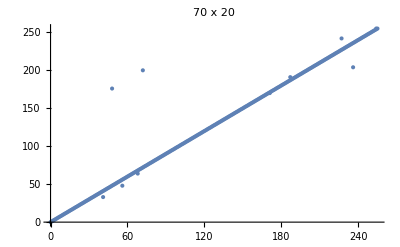

```mathematica
Block[{W=70,H=20,netTemp,pts},netTemp=netTrainedWCA[W,H];
pts=Flatten[Table[{i,netTemp[RandomRule[i,W,H]]},{i,0,255},{50}],1]//Union;
ListPlot[pts,FrameLabel->{"Correct Rule","Predicted Rule"},PlotLabel->StringTemplate["`1` x `2`"][W,H]]]
```